```mathematica
Ln1=4;
Ln2=1;
com1=1;
com2=2;
```

P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+c*γ))^(l1+l2)((c*γ)/(2+c*γ))^c
```

P(l1<L1,l2=L2)

```mathematica
P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*(c*γ)^c/(c*γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*(c*γ)^c/(c*γ+2)^(l1+l2+c),{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
```

Note that also L2 Cannot be less than 1.

Entropy

```mathematica
En[L1_,L2_,c_,γ_]:=-Sum[Sum[P1[l1,l2,c,γ]*Log[P1[l1,l2,c,γ]],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ]*Log[P2[l1,L2,c,γ]],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ]*Log[P2[l2,L1,c,γ]],{l2,0,L2-1}]-P3[L1,L2,c,γ]*Log[P3[L1,L2,c,γ]]
```

For comparison P(l<L, c=1)

```mathematica
P11[l_,p_]:=(1-p)* p^l
```

P(l=L,c=1)

```mathematica
P21[L_,p_]:=p^L
```

Entropy c=1

```mathematica
EN[L_,p_]:=-(Sum[P11[l,p]*Log[P11[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

Perfect Clock P(l1,l2<L1,L2)

```mathematica
Pc1[l1_,l2_,t_]:=Exp[-2*t]*t^(l1+l2)/(l1!l2!)
Pc2[l1_,L2_,t_]:=t^l1/(l1!)*Exp[-t]*(1-Exp[-t]*Sum[t^l2/(l2!),{l2,0,L2-1}])
Pc3[L1_,L2_,t_]:=1-Sum[Sum[Pc1[l1,l2,t],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[Pc2[l1,L2,t],{l1,0,L1-1}]-Sum[Pc2[l2,L1,t],{l2,0,L2-1}]
ENPC[L1_,L2_,t_]:=-(Sum[Sum[Pc1[l1,l2,t]*Log[Pc1[l1,l2,t]],{l1,0,L1-2}],{l2,0,L2-1}]+Sum[Pc2[l1,L2,t]*Log[Pc2[l1,L2,t]],{l1,0,L1-1}]+Sum[Pc2[l2,L1,t]*Log[Pc2[l2,L2,t]],{l2,0,L2-1}]+Pc3[L1,L2,t]*Log[Pc3[L1,L2,t]])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

Relative Entropies!

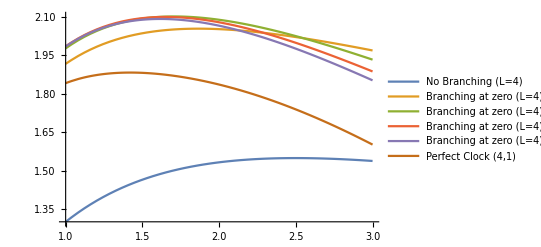

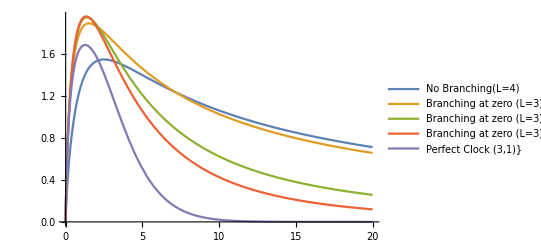

```mathematica
Plot[{EN[4,h[τ]],En[4,1,1,1/τ], En[4,1,2,1/τ],En[4,1,3,1/τ],En[4,1,4,1/τ],ENPC[4,1,τ]},{τ,1,3},PlotLegends->{"No Branching (L=4)","Branching at zero (L=4) c=1","Branching at zero (L=4) c=2","Branching at zero (L=4) c=3","Branching at zero (L=4) c=4","Perfect Clock (4,1)"}]
Plot[{EN[4,h[τ]],En[3,1,1,1/τ], En[3,1,2,1/τ],En[3,1,3,1/τ],ENPC[3,1,τ]},{τ,0,20},PlotLegends->{"No Branching(L=4) ","Branching at zero (L=3) c=1","Branching at zero (L=3) c=2","Branching at zero (L=3) c=3","Perfect Clock (3,1)}"}]
```

Yields of Each Species, especially comparing Terminating Structures

```mathematica
c=1;
```

```mathematica
T1=Evaluate@Table[P1[l1,l2,c,1/τ], {l1,0,Ln1-1},{l2,0,Ln2-1}]; 
T2=Evaluate@Table[P2[l1,Ln2,c,1/τ],{l1,0,Ln1-1}];
T3=Evaluate@Table[P2[l1,Ln1,c,1/τ],{l1,0,Ln2-1}];
```

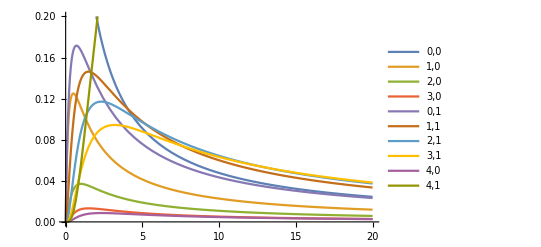

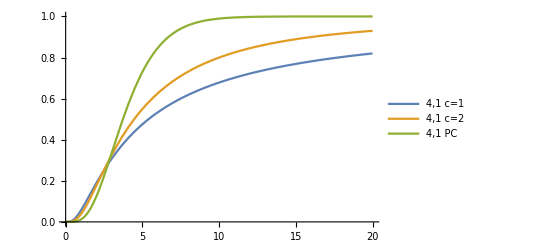

-Graphics-

```mathematica
Plot1=Plot[{T1,T2,T3,P3[Ln1,Ln2,c,1/τ]},{τ,0,20}, PlotRange->{0,0.2},PlotLegends->{"0,0","1,0","2,0","3,0","0,1","1,1","2,1","3,1","4,0","4,1"}]
Plot2=Plot[{P3[Ln1,Ln2,c,1/τ],P3[Ln1,Ln2,2,1/τ],Pc3[Ln1,Ln2,τ]},{τ,0,20},PlotLegends->{"4,1 c=1","4,1 c=2","4,1 PC"}]
Plot3=Plot[{P2[3,Ln2,c,1/τ],P2[3,Ln2,2,1/τ],Pc2[3,1,τ]},{τ,0,20},PlotLegends->{"3,1 c=1","3,1 c=2","3,1 PC"},PlotRange->{0,0.25}];
Plot4=Plot[{P2[2,Ln2,c,1/τ],P2[2,Ln2,2,1/τ],Pc2[2,1,τ]},{τ,0,20},PlotLegends->{"2,1 c=1","2,1 c=2","2,1 PC"},PlotRange->{0,0.25}];
Plot5=Plot[{P2[1,Ln2,c,1/τ],P2[1,Ln2,2,1/τ],Pc2[1,1,τ]},{τ,0,20},PlotLegends->{"1,1 c=1","1,1 c=2","1,1 PC"},PlotRange->{0,0.3}];
Plot6=Plot[{P2[0,Ln2,c,1/τ],P2[0,Ln2,2,1/τ],Pc2[0,1,τ]},{τ,0,20},PlotLegends->{"0,1 c=1","0,1 c=2","0,1 PC"},PlotRange->{0,0.3}];
Plot7=Plot[{P2[0,Ln1,c,1/τ],P2[0,Ln1,2,1/τ],Pc2[0,4,τ]},{τ,0,20},PlotLegends->{"4,0 c=1","4,0 c=2","4,0 PC"},PlotRange->{0,0.07}];
Plot8=Plot[{P1[0,3,c,1/τ],P1[0,3,2,1/τ],Pc1[3,0,τ]},{τ,0,20},PlotLegends->{"3,0 c=1","3,0 c=2","3,0 PC"},PlotRange->{0,0.07}];
Plot9=Plot[{P1[0,2,c,1/τ],P1[0,2,2,1/τ],Pc1[2,0,τ]},{τ,0,20},PlotLegends->{"2,0 c=1","3,0 c=2","2,0 PC"},PlotRange->{0,0.21}];
Plot10=Plot[{P1[0,1,c,1/τ],P1[0,1,2,1/τ],Pc1[1,0,τ]},{τ,0,20},PlotLegends->{"1,0 c=1","0,0 c=2","1,0 PC"},PlotRange->{0,0.21}];
Plot11=Plot[{P1[0,0,c,1/τ],P1[0,0,2,1/τ],Pc1[0,0,τ]},{τ,0,20},PlotLegends->{"0,0 c=1","0,0 c=2","0,0 PC"},PlotRange->{0,1}];

GraphicsGrid[{{Plot3,Plot4},{Plot5,Plot6},{Plot7,Plot8},{Plot9,Plot10}},Spacings->{0,0}]
```

Yields of Each Species Out of P=1 total

```mathematica
NT1=Length[T1];
NT2=Length[T2]
NT3=Length[T3]

T12=Evaluate@Table[Sum[T1[[{i}]],{i,1,j}],{j,1,NT1}];
T22=Evaluate@Table[T12[[NT1]]+Sum[T2[[{i}]],{i,1,j}],{j,1,NT2}];
T32=Evaluate@Table[T22[[NT2]]+Sum[T3[[{i}]],{i,1,j}],{j,1,NT3}];
CU1[L1_,L2_,c_,γ_]:=T32[[NT3]]+P3[L1,L2,c,γ];
```

4

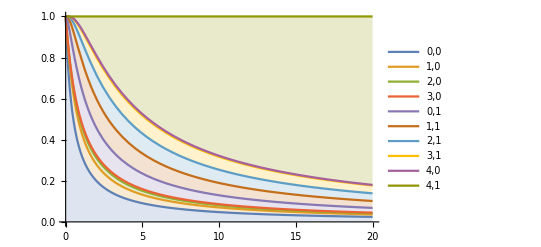

```mathematica
Plot[{T12,T22,T32,CU1[Ln1,Ln2,1,1/τ]},{τ,0,20},Filling->{1->Axis,2->{1},3->{2},4->{3},5->{4},6->{5},7->{6},8->{7},9->{8},10->{9}},PlotLegends->{"0,0","1,0","2,0","3,0","0,1","1,1","2,1","3,1","4,0","4,1"}]
```

One compartment >5%

```mathematica
T13=Evaluate@Table[τ/.Solve[P1[l1,l2,com1,1/τ]==1/20&& τ>0],{l1,0,Ln1-1},{l2,0,Ln2-1}];
T23=Evaluate@Table[τ/.Solve[P2[l1,Ln2,com1,1/τ]==1/20&&τ>0],{l1,0,Ln1-1}];
T33=Evaluate@Table[τ/.Solve[P2[l1,Ln1,com1,1/τ]==1/20&&τ>0],{l1,0,Ln2-1}];
```

```mathematica
T43=τ/.Solve[P3[Ln1,Ln1,com1,1/τ]==1/20&&τ>0];
```

```mathematica
Flatten[{T13,T23,T33,T43}]
```

{19/2,1/2 (4-√15),1/2 (4+√15),τ,τ,1/4 (17-√281),1/4 (17+√281),Root[1+6 #1-27 #1^2-48 #1^3+4 #1^4&,3],Root[1+6 #1-27 #1^2-48 #1^3+4 #1^4&,4],Root[1+9 #1+33 #1^2+3 #1^3-114 #1^4-104 #1^5+8 #1^6&,1],Root[1+9 #1+33 #1^2+3 #1^3-114 #1^4-104 #1^5+8 #1^6&,2],Root[1+12 #1+62 #1^2+180 #1^3+241 #1^4-312 #1^6-204 #1^7+16 #1^8&,3],Root[1+12 #1+62 #1^2+180 #1^3+241 #1^4-312 #1^6-204 #1^7+16 #1^8&,4],τ,Root[-1-18 #1-146 #1^2-704 #1^3-2241 #1^4-4942 #1^5-7700 #1^6-8472 #1^7-5048 #1^8+1808 #1^9+5200 #1^10+2432 #1^11&,3]}

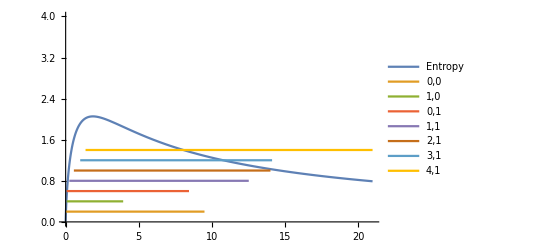

```mathematica
a[x_]:=0.2/;x<19/2
b[x_]:=0.4/;T13[[2]][[1]][[1]]<x<T13[[2]][[1]][[2]]
d[x_]:=0.6/;T23[[1]][[1]]<x<T23[[1]][[2]]
e[x_]:=0.8/;T23[[2]][[1]]<x<T23[[2]][[2]]
f[x_]:=1/;T23[[3]][[1]]<x<T23[[3]][[2]]
g[x_]:=1.2/;T23[[4]][[1]]<x<T23[[4]][[2]]
i[x_]:=1.4/;T43[[1]]<x
Plot[{En[Ln1,Ln2,c,1/x],a[x],b[x],d[x],e[x],f[x],g[x],i[x]},{x,0,21},PlotRange->{0,4}, PlotLegends->{"Entropy","0,0","1,0","0,1","1,1","2,1","3,1","4,1"}]
```

Two Compartments >5%

```mathematica
T132=Evaluate@Table[τ/.Solve[P1[l1,l2,2,1/τ]==1/20&& τ>0],{l1,0,Ln1-1},{l2,0,Ln2-1}];
T232=Evaluate@Table[τ/.Solve[P2[l1,Ln2,2,1/τ]==1/20&&τ>0],{l1,0,Ln1-1}];
T332=Evaluate@Table[τ/.Solve[P2[l1,Ln1,2,1/τ]==1/20&&τ>0],{l1,0,Ln2-1}]

T432=τ/.Solve[P3[Ln1,Ln1,2,1/τ]==1/20&&τ>0]
```

{τ}

{Root[-128-1344 #1-6464 #1^2-18848 #1^3-37160 #1^4-52292 #1^5-54016 #1^6-41456 #1^7-17332 #1^8+5870 #1^9+12386 #1^10+6473 #1^11+1368 #1^12+76 #1^13&,3]}

```mathematica
a1[x_]:=0.2/;x<T132[[1]][[1]][[1]]
b1[x_]:=0.4/;T132[[2]][[1]][[1]]<x<T132[[2]][[1]][[2]]
d1[x_]:=0.6/;T232[[1]][[1]]<x<T232[[1]][[2]]
e1[x_]:=0.8/;T232[[2]][[1]]<x<T232[[2]][[2]]
f1[x_]:=0.1/;T232[[3]][[1]]<x<T232[[3]][[2]]
g1[x_]:=1.2/;T232[[4]][[1]]<x<T232[[4]][[2]]
i1[x_]:=1.4/;T432[[1]]<x
```

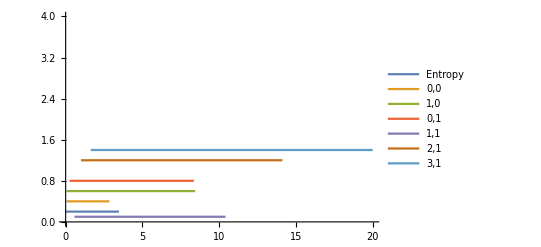

```mathematica
Plot[{a1[x],b1[x],d[1x],e1[x],f1[x],g[1x],i1[x]},{x,0,20},PlotRange->{0,4}, PlotLegends->{"Entropy","0,0","1,0","0,1","1,1","2,1","3,1","4,1"}]
```

Maximums of Entropy

{{1.8657,2.05429},{1.70715,2.102},{1.64952,2.10009},{1.61676,2.09226},{1.59473,2.08448},{1.57861,2.07774},{1.56618,2.07206},{1.55626,2.06728},{1.54813,2.06324},{1.54134,2.05978},{1.53558,2.0568},{1.53063,2.05421},{1.52632,2.05194},{1.52253,2.04993},{1.51919,2.04815},{1.5162,2.04655},{1.51352,2.04512},{1.51111,2.04382},{1.50891,2.04265},{1.50692,2.04157}}

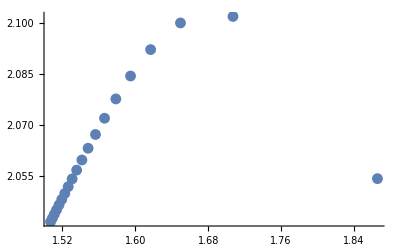

```mathematica
MaxX=Flatten[Evaluate@Table[FindArgMax[Simplify[En[4,1,c,1/τ]],{τ,0.1,2}],{c,1,20}]];
MaxY=Flatten[Evaluate@Table[FindMaxValue[Simplify[En[4,1,c,1/τ]],{τ,0.1,2}],{c,1,20}]];
MaxEnt=Transpose[{MaxX,MaxY}]
ListPlot[MaxEnt]
```

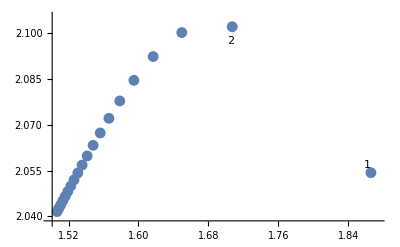

-Graphics-